## Estimation of Coupled Exponential Distribution

### Plot of equations of GeoMean, mean of pairs, second moment of triplets.

From notes by Amaneh Al-Najafi

Correction: the equation for G (geometric mean), the sign of κ needs to be reversed. This changes the equation to reference from the paper by Vogel to:
G = (σ μ)/κ Exp[PolyGamma[1]-PolyGamma[1+1/κ]+κ]

The results below are based on Amenah’s derivation; however, the Mathematica derivation showed  a difference, so this section will eventually be modified.

```mathematica
$Assumptions=={μ,σ,κ}∈Reals&&0<σ<∞&&0<κ<∞&&0<=p<=1
```

True=={μ,σ,κ}∈ℝ&&0<σ<∞&&0<κ<∞&&0≤p≤1

```mathematica
Clear[CoupledExponentialEstimators,GeoMean,MeanPairs,SecondMomentTriplets];
CoupledExponentialEstimators[GeoMean_,MeanPairs_,SecondMomentTriplets_]:=
{
GeoMean==(σ μ)/κ Exp[PolyGamma[1]-PolyGamma[1+1/κ]+κ],
MeanPairs==μ+σ/2,
SecondMomentTriplets==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ))
}
```

```mathematica
ContourPlot3D[Evaluate@CoupledExponentialEstimators[2.72,2.25,0.424],
{μ,0,4},{σ,0,2},{κ,0,3},
AxesLabel->{μ,σ,κ},
PlotLegends->{"GeoMean","MeanPairs","SecondMomentTriplets"}]
```

-Graphics3D-

```mathematica
ContourPlot3D[Evaluate@CoupledExponentialEstimators[3.17,2.25,4.15],
{μ,0,4},{σ,0,2},{κ,0,3},
AxesLabel->{μ,σ,κ},
PlotLegends->{"GeoMean","MeanPairs","SecondMomentTriplets"}]
```

-Graphics3D-

```mathematica
ContourPlot3D[Evaluate@CoupledExponentialEstimators[4.98,2.25,5589],
{μ,0,4},{σ,0,2},{κ,0,3},
AxesLabel->{μ,σ,κ},
PlotLegends->{"GeoMean","MeanPairs","SecondMomentTriplets"}]
```

-Graphics3D-

### Derivation of the GeoMean of the Coupled Exponential Distribution

#### Assuming μ = 0

The Quantile function of the Coupled Exponential Distribution
If[κ!=0,-σ/κ(1-(1-p)^-κ),
-σ Log[1-p]
]
simplifies to σ CoupledLogarithm[(1-p)^-1,κ]

```mathematica
ClearAll[p,κ];
```

```mathematica
ClearAll[CoupledExponentialQuantileFunction];
CoupledExponentialQuantileFunction[p_,μ_:0,σ_,κ_]:=
CoupledExponentialQuantileFunction[p,μ,σ,κ]=σCoupledLogarithm[(1-p)^-1,κ,0]
```

Test Quantile Function

```mathematica
CoupledExponentialQuantileFunction[0.999,0,1,-0.5]
```

1.93675

```mathematica
If[κ!=0,-σ/κ(1-(1-p)^-κ),
-σ Log[1-p]
]/.{p->0.999,σ->1,κ->-0.5}
```

1.93675

Integration of Quantile Function to form Geometric Mean

```mathematica
FullSimplify@Exp[∫_0^1 FullSimplify@Log@CoupledExponentialQuantileFunction[p,0,σ,κ]ⅆp]
```

ⅇ^(∫_0^1 ConditionalExpression[Piecewise[{{Log[((-1+(1-p)^-κ) σ)/κ], κ≠0}, {Log[-σ Log[1-p]], True}}], p<1]ⅆp)

```mathematica
Assuming[0<κ<∞,FullSimplify@Exp[∫_0^1 FullSimplify@Log[((-1+(1-p)^-κ) σ)/κ]ⅆp]]
```

(ⅇ^(-HarmonicNumber[-1+1/κ]) σ)/κ

```mathematica
Assuming[-1<κ<0,FullSimplify@Exp[∫_0^1 FullSimplify@Log[((-1+(1-p)^-κ) σ)/κ]ⅆp]]
```

-(ⅇ^(κ-HarmonicNumber[-(1+κ)/κ]) σ)/κ

```mathematica
FullSimplify@Exp[∫_0^1 Log[- σ Log[1-p]]ⅆp]
```

ⅇ^-EulerGamma σ

The Harmonic number and the Digamma functions have the following relationship. 
H_z=ψ(z+1)-γ where γ is the Euler gamma constant 0.5172216...

See this Wolfram Research article on the history.
https://functions.wolfram.com/GammaBetaErf/HarmonicNumber2/introductions/DifferentiatedGammas/ShowAll.html

Summarizing Result

GeometricMean of Coupled Exponential =
Piecewise[{{(ⅇ^(-HarmonicNumber[-1+1/κ]) σ)/κ, κ>0}, {-(ⅇ^(κ-HarmonicNumber[-(1+κ)/κ]) σ)/κ, -1<κ<0}, {ⅇ^-EulerGamma σ, κ=0}}]

#### Assuming μ ≠ 0

```mathematica
ClearAll[CoupledExponentialQuantileFunction];
CoupledExponentialQuantileFunction[p_,μ_,σ_,κ_]:=
CoupledExponentialQuantileFunction[p,μ,σ,κ]=μ+σCoupledLogarithm[(1-p)^-1,κ,0]
```

```mathematica
Assuming[0<κ<∞&&μ∈Reals,FullSimplify@Exp[∫_0^1 FullSimplify@Log[μ+((-1+(1-p)^-κ) σ)/κ]ⅆp]]
```

ConditionalExpression[ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ, μ≥0]

```mathematica
Assuming[-1<κ<0&&μ∈Reals,FullSimplify@Exp[∫_0^1 FullSimplify@Log[μ+((-1+(1-p)^-κ) σ)/κ]ⅆp]]
```

ConditionalExpression[ⅇ^(-π (-1+(κ μ)/σ)^(-1/κ) Csc[π/κ]+κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ, μ≥0]

```mathematica
Assuming[0<μ<∞&&μ<σ<∞,FullSimplify@Exp[∫_0^1 Log[μ- σ Log[1-p]]ⅆp]]
```

ⅇ^(-ⅇ^(μ/σ) ExpIntegralEi[-μ/σ]) μ

There is no simplification to the solution by assuming 0<μ<∞ && μ<σ<∞

```mathematica
Assuming[0<κ<∞&&0<μ<∞&&μ<σ<∞,FullSimplify@Exp[∫_0^1 FullSimplify@Log[μ+((-1+(1-p)^-κ) σ)/κ]ⅆp]]
```

ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ

```mathematica
Assuming[-1<κ<0&&0<μ<∞&&μ<σ<∞,FullSimplify@Exp[∫_0^1 FullSimplify@Log[μ+((-1+(1-p)^-κ) σ)/κ]ⅆp]]
```

ⅇ^(∫_0^1 Log[μ+((-1+(1-p)^-κ) σ)/κ]ⅆp)

Check relationship with equation solved by Amenah; there does seem to be a difference

```mathematica
FullSimplify[(μ σ)/κ Exp[PolyGamma[1]-PolyGamma[1+1/κ]],0<κ<∞&&0<=μ<∞&&0<σ<∞]
```

(ⅇ^(-HarmonicNumber[1/κ]) μ σ)/κ

```mathematica
FullSimplify[ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]),0<κ<∞]
```

ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ])

```mathematica
FullSimplify[Limit[ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ])μ,μ->0],0<κ<∞]
```

(ⅇ^(-HarmonicNumber[-1+1/κ]) σ)/κ

```mathematica
FullSimplify[Limit[ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ])μ,κ->0],μ>=0]
```

lim_(κ→0) ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ

Summarizing Result

GeometricMean of Coupled Exponential
Assuming μ>=0 && σ>μ
Piecewise[{{ConditionalExpression[ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ, μ≥0], κ>0}, {ConditionalExpression[ⅇ^(-π (-1+(κ μ)/σ)^(-1/κ) Csc[π/κ]+κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ, μ≥0], -1<κ<0}, {ⅇ^(-ⅇ^(μ/σ) ExpIntegralEi[-μ/σ]) μ, κ=0}}]

### Reduction of Equations

```mathematica
Solve[
{
GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ,
MeanPairs==μ+σ/2,
SecondMomentTriplets==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ))
},{μ,σ,κ},Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ,MeanPairs==μ+σ/2,SecondMomentTriplets==μ^2+(2 μ σ)/(3+κ)+(2 σ^2)/(3 (3+κ))},{μ,σ,κ},ℝ]

Fix mistake in next equation

```mathematica
μ==MeanPairs-σ/2
```

```mathematica
Solve[
{
GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (MeanPairs-σ/2))/σ]) (MeanPairs-σ/2),
SecondMomentTriplets==(MeanPairs-σ/2)^2+(2(MeanPairs-σ/2) σ)/(3+κ)+(2 σ^2)/(3(3+κ))
},{σ,κ},Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (MeanPairs-σ/2))/σ]) (MeanPairs-σ/2),SecondMomentTriplets==(MeanPairs-σ/2)^2+(2 (MeanPairs-σ/2) σ)/(3+κ)+(2 σ^2)/(3 (3+κ))},{σ,κ},ℝ]

```mathematica
SolveValues[
{
GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (MeanPairs-σ/2))/σ]) (MeanPairs-σ/2),
SecondMomentTriplets==(MeanPairs-σ/2)^2+(2(MeanPairs-σ/2) σ)/(3+κ)+(2 σ^2)/(3(3+κ))
},{σ,κ},Reals]
```

SolveValues::nsmet: This system cannot be solved with the methods available to SolveValues.

SolveValues[{GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (MeanPairs-σ/2))/σ]) (MeanPairs-σ/2),SecondMomentTriplets==(MeanPairs-σ/2)^2+(2 (MeanPairs-σ/2) σ)/(3+κ)+(2 σ^2)/(3 (3+κ))},{σ,κ},ℝ]

```mathematica
SolveValues[
GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (MeanPairs-σ/2))/σ]) (MeanPairs-σ/2),
σ,Reals]
```

SolveValues::nsmet: This system cannot be solved with the methods available to SolveValues.

SolveValues[GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (MeanPairs-σ/2))/σ]) (MeanPairs-σ/2),σ,ℝ]

```mathematica
Solve[
SecondMomentTriplets==(MeanPairs-σ/2)^2+(2(MeanPairs-σ/2) σ)/(3+κ)+(2 σ^2)/(3(3+κ)),
σ,Reals]
```

```mathematica
{{σ->ConditionalExpression[(6 (MeanPairs+MeanPairs κ))/(5+3 κ)-2 √3 √(1/(5+3 κ)^2(-12 MeanPairs^2+15 SecondMomentTriplets-8 MeanPairs^2 κ+14 SecondMomentTriplets κ+3 SecondMomentTriplets κ^2)), (SecondMomentTriplets>(12 MeanPairs^2+8 MeanPairs^2 κ)/(15+14 κ+3 κ^2)&&κ>-5/3)||(-3<κ<-5/3&&SecondMomentTriplets<(12 MeanPairs^2+8 MeanPairs^2 κ)/(15+14 κ+3 κ^2))||(κ<-3&&SecondMomentTriplets>(12 MeanPairs^2+8 MeanPairs^2 κ)/(15+14 κ+3 κ^2))]},{σ->ConditionalExpression[(6 (MeanPairs+MeanPairs κ))/(5+3 κ)+2 √3 √(1/(5+3 κ)^2(-12 MeanPairs^2+15 SecondMomentTriplets-8 MeanPairs^2 κ+14 SecondMomentTriplets κ+3 SecondMomentTriplets κ^2)), (SecondMomentTriplets>(12 MeanPairs^2+8 MeanPairs^2 κ)/(15+14 κ+3 κ^2)&&κ>-5/3)||(-3<κ<-5/3&&SecondMomentTriplets<(12 MeanPairs^2+8 MeanPairs^2 κ)/(15+14 κ+3 κ^2))||(κ<-3&&SecondMomentTriplets>(12 MeanPairs^2+8 MeanPairs^2 κ)/(15+14 κ+3 κ^2))]}}
```

Simplify expression in terms of κ

```mathematica
FullSimplify[GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (MeanPairs-((6 (MeanPairs+MeanPairs κ))/(5+3 κ)-2 √3 √(1/(5+3 κ)^2(-12 MeanPairs^2+15 SecondMomentTriplets-8 MeanPairs^2 κ+14 SecondMomentTriplets κ+3 SecondMomentTriplets κ^2)))/2))/((6 (MeanPairs+MeanPairs κ))/(5+3 κ)-2 √3 √(1/(5+3 κ)^2(-12 MeanPairs^2+15 SecondMomentTriplets-8 MeanPairs^2 κ+14 SecondMomentTriplets κ+3 SecondMomentTriplets κ^2)))]) (MeanPairs-1/2((6 (MeanPairs+MeanPairs κ))/(5+3 κ)-2 √3 √(1/(5+3 κ)^2(-12 MeanPairs^2+15 SecondMomentTriplets-8 MeanPairs^2 κ+14 SecondMomentTriplets κ+3 SecondMomentTriplets κ^2))))]
```

1/(5+3 κ)ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,(-2 MeanPairs (3+2 κ)+(2+κ) (5+3 κ) √(SecondMomentTriplets+(4 MeanPairs^2)/(5+3 κ)^2+(4 (-2 MeanPairs^2+SecondMomentTriplets))/(5+3 κ)))/(-6 MeanPairs (1+κ)+2 (5+3 κ) √(SecondMomentTriplets+(4 MeanPairs^2)/(5+3 κ)^2+(4 (-2 MeanPairs^2+SecondMomentTriplets))/(5+3 κ)))]) (2 MeanPairs+(5+3 κ) √(SecondMomentTriplets+(4 MeanPairs^2)/(5+3 κ)^2+(4 (-2 MeanPairs^2+SecondMomentTriplets))/(5+3 κ)))==GeoMean

### Contour Plots

```mathematica
Manipulate[
ContourPlot3D[
1/(5+3 κ)ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,(-2 MeanPairs (3+2 κ)+(2+κ) (5+3 κ) √(SecondMomentTriplets+(4 MeanPairs^2)/(5+3 κ)^2+(4 (-2 MeanPairs^2+SecondMomentTriplets))/(5+3 κ)))/(-6 MeanPairs (1+κ)+2 (5+3 κ) √(SecondMomentTriplets+(4 MeanPairs^2)/(5+3 κ)^2+(4 (-2 MeanPairs^2+SecondMomentTriplets))/(5+3 κ)))]) (2 MeanPairs+(5+3 κ) √(SecondMomentTriplets+(4 MeanPairs^2)/(5+3 κ)^2+(4 (-2 MeanPairs^2+SecondMomentTriplets))/(5+3 κ)))==GeoMean,
{GeoMean,0,5},{MeanPairs,0,5},{SecondMomentTriplets,0,5},
AxesLabel->{"MeanPairs","SecondMomentTriplets","GeoMean"}],
{{κ,1},0,2}
]
```

```mathematica
Manipulate[
ContourPlot3D[
Evaluate[{
GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ,
MeanPairs==μ+σ/2,
SecondMomentTriplets==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ))
}],
{GeoMean,0,5},{MeanPairs,0,5},{SecondMomentTriplets,0,5},
AxesLabel->{"GeoMean","MeanPairs","SecondMomentTriplets"},
PlotLegends->{"GeoMean","MeanPairs","SecondMomentTriplets"}],
{{μ,0.1},0,2},{{σ,1},0,10},{{κ,0.5},0,2}
]
```

```mathematica
ContourPlot3D[GeoMeanCE[μ,σ,κ],{μ,0,1},{σ,0,5},{κ,0,2}]
```

$Aborted

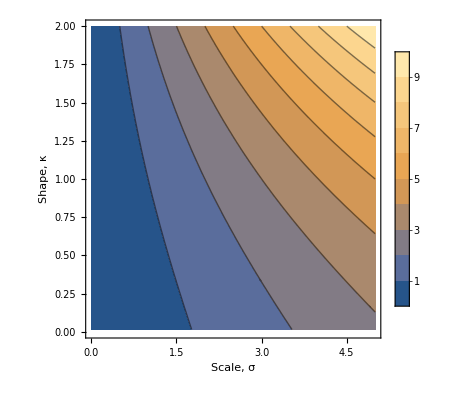

```mathematica
ContourPlot[GeoMeanCE[0,σ,κ],{σ,0,5},{κ,0,2},
PlotLegends->Automatic,
FrameLabel->{"Scale, σ","Shape, κ"}]
```

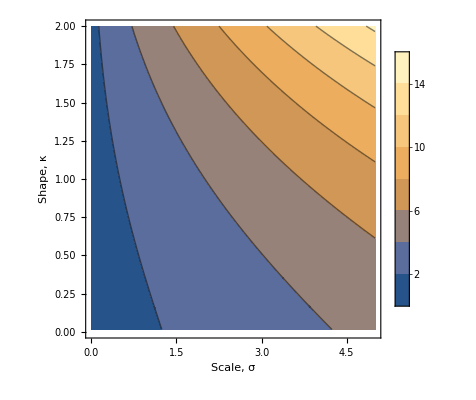

```mathematica
ContourPlot[GeoMeanCE[1,σ,κ],{σ,0,5},{κ,0,2},
PlotLegends->Automatic,
FrameLabel->{"Scale, σ","Shape, κ"}]
```

#### Contour Plots for distribution parameters given moment estimations

Attempts to use the Manipulate control result in aborted computation

```mathematica
Manipulate[
ContourPlot3D[
Evaluate[{
ⅇ^(κS Hypergeometric2F1[1,1/κS,1+1/κS,1-(κS μS)/σS]) μS==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ,
μS+σS/2==μ+σ/2,
μS^2+(2μS σS)/(3+κS)+(2 σS^2)/(3(3+κS))==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ))
}],
{μ,0,4},{σ,0,1.1},{κ,0,2},
AxesLabel->{"μ","σ","κ"},
PlotLegends->{"GeoMean","MeanPairs","SecondMomentTriplets"}],
{{μS,0.1},0,5},{{σS,1},0,10},{{κS,0.5},0,2}
]
```

General::munfl: 0.1375^6999999 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.94477×10^-301)/-335997648 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(4.85853×10^-307)/342997550 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.1375^6999999 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.94477×10^-301)/-335997648 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(4.85853×10^-307)/342997550 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.1375^6999999 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.94477×10^-301)/-335997648 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(4.85853×10^-307)/342997550 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.1375^6999999 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.94477×10^-301)/-335997648 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(4.85853×10^-307)/342997550 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.1375^6999999 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.94477×10^-301)/-335997648 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(4.85853×10^-307)/342997550 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.1375^6999999 is too small to represent as a normalized machine number; precision may be lost.

First compute a set of moments

```mathematica
Manipulate[
Evaluate[{
ⅇ^(κS Hypergeometric2F1[1,1/κS,1+1/κS,1-(κS μS)/σS]) μS==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ,
μS+σS/2==μ+σ/2,
μS^2+(2μS σS)/(3+κS)+(2 σS^2)/(3(3+κS))==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ))
}],
{{μS,0.1},0,5},{{σS,1},0,10},{{κS,0.5},0,2}
]
```

Try Contour Maps from simplest to hardest curve individually

```mathematica
CEEstimationPlot[Equation_,EquationLabel_]:=ContourPlot3D[
Evaluate[Equation],
{μ,0,4},{σ,0,1.1},{κ,0,2},
AxesLabel->{"μ","σ","κ"},
PlotLegends->{EquationLabel},
PlotLabel->"μ=2, σ=3, κ=1"]
```

```mathematica
CEEstimationPlot[7/2==μ+σ/2,"MeanPairs"]
```

-Graphics3D-

```mathematica
CEEstimationPlot[17/2==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ)),"SecondMomentTriplets"]
```

-Graphics3D-

```mathematica
CEEstimationPlot[27/4==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ,"GeoMean"]
```

General::munfl: 0.1375^6999999 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.94477×10^-301)/-335997648 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(4.85853×10^-307)/342997550 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

Not sure why the 3D contour plot for the MeanPair and SecondMomentTriplets does not show an intersection but presumably it has something to do with the internal contour parameter settings

```mathematica
ContourPlot3D[
Evaluate[{
7/2==μ+σ/2,
17/2==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ))
}],
{μ,0,4},{σ,0,1.1},{κ,0,2},
AxesLabel->{"μ","σ","κ"},
PlotLegends->{"MeanPairs","SecondMomentTriplets"},
PlotLabel->"μ=2, σ=3, κ=1"]
```

-Graphics3D-

2D Plots do show clear intersections

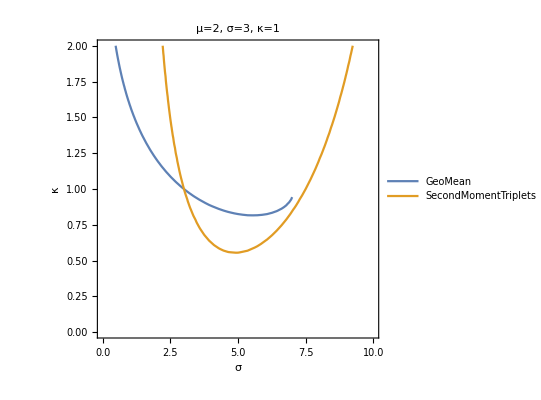

```mathematica
ContourPlot[{27/4==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (7/2-σ/2))/σ]) (7/2-σ/2),17/2==(7/2-σ/2)^2+(2 (7/2-σ/2) σ)/(3+κ)+(2 σ^2)/(3 (3+κ))},
{σ,0,10},{κ,0,2},
FrameLabel->{"σ","κ"},
PlotLegends->{"GeoMean","SecondMomentTriplets"},
PlotLabel->"μ=2, σ=3, κ=1"]
```

#### Saved Plots

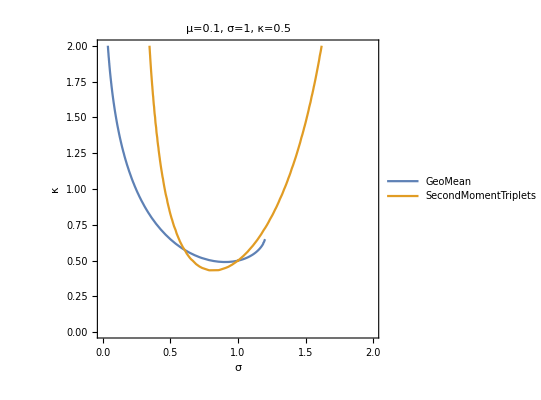

-Graphics-

Find Minimum of SecondMomentTriples with respect to κ

```mathematica
Solve[17/2==(7/2-σ/2)^2+(2 (7/2-σ/2) σ)/(3+κ)+(2 σ^2)/(3 (3+κ)),κ]
```

{{κ→(-135+42 σ-5 σ^2)/(3 (15-14 σ+σ^2))}}

```mathematica
FindMinimum[(-135+42 σ-5 σ^2)/(3 (15-14 σ+σ^2)),{σ,1}]
```

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{-4.3368×10^14,{σ→1.16905}}

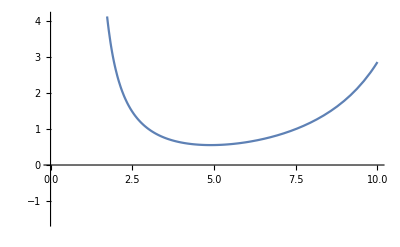

```mathematica
Plot[(-135+42 σ-5 σ^2)/(3 (15-14 σ+σ^2)),{σ,0,10}, PlotRange->Automatic]
```

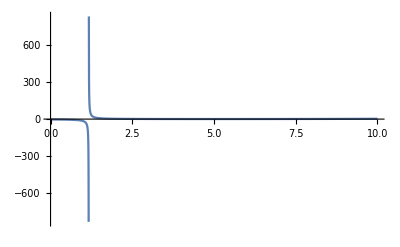

```mathematica
Plot[(-135+42 σ-5 σ^2)/(3 (15-14 σ+σ^2)),{σ,0,10}, PlotRange->Full]
```

```mathematica
FindMinimum[(-135+42 σ-5 σ^2)/(3 (15-14 σ+σ^2)),{σ,2}]
```

{0.554805,{σ→4.89929}}

So there are some challenges with the search for σ and κ if the search does not seed a value close to the solution. In particular the zero of (15-14 σ+σ^2) causes κ to go to infinity.  It’s important to be the side that produces a positive kappa

### Algorithm Prototype for Estimating Coupled Exponentials

#### Compute Moments

This section will be replaced with drawing of samples and estimation of the moments

```mathematica
Clear[GeoMeanCE,MeanPairsCE,SecondMomentTripletsCE];
SetAttributes[{"GeoMeanCE","MeanPairsCE","SecondMomentTripletsCE"},Listable];
GeoMeanCE[μ_,σ_,κ_]:=GeoMeanCE[μ,σ,κ]=
Piecewise[{{Piecewise[{{ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ])μ, κ>0}, {ⅇ^(-π (-1+(κ μ)/σ)^(-1/κ) Csc[π/κ]+κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ, -1<=κ<0}, {ⅇ^(-ⅇ^(μ/σ) ExpIntegralEi[-μ/σ]) μ, κ==0}, {"Not a Distribution", True}}], μ>0}, {Piecewise[{{(ⅇ^(-HarmonicNumber[-1+1/κ]) σ)/κ, κ>0}, {-(ⅇ^(κ-HarmonicNumber[-(1+κ)/κ]) σ)/κ, -1<=κ<0}, {ⅇ^-EulerGamma σ, κ==0}, {"Not a Distribution", True}}], μ==0}, {"Not a Distribution", True}}];
MeanPairsCE[μ_,σ_]:=MeanPairsCE[μ,σ]=
μ+σ/2;
SecondMomentTripletsCE[μ_,σ_,κ_]:=SecondMomentTripletsCE[μ,σ,κ]=
μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ));
```

```mathematica
CEParameters = <|
"Location" ->{0,1,2,0.5},
"Scale" ->{1,2,3,1.5},
"Shape" ->{0.2,0.45,1.2,2.3}
|>
CEMoments =
{GeoMeanCE[#Location,#Scale,#Shape],MeanPairsCE[#Location,#Scale],SecondMomentTripletsCE[#Location,#Scale,#Shape]}&[
CEParameters
]
```

<|Location→{0,1,2,0.5},Scale→{1,2,3,1.5},Shape→{0.2,0.45,1.2,2.3}|>

{{0.622572,3.02864,7.52959,6.0277},{1/2,2,7/2,1.25},{0.208333,2.93237,8.28571,0.816038}}

#### Numerical Solution of Parameters given Estimates

```mathematica
Clear[EstimateCEParameters];
SetAttributes[EstimateCEParameters,Listable];
EstimateCEParameters[GeoMeanEst_,MeanPairEst_,SecondMomentTripletsEst_]:=
EstimateCEParameters[GeoMeanEst,MeanPairEst,SecondMomentTripletsEst]=
NSolve[
{GeoMeanEst==GeoMeanCE[μ,σ,κ],
MeanPairEst==MeanPairsCE[μ,σ],
SecondMomentTripletsEst=SecondMomentTripletsCE[μ,σ,κ]
},
{μ,σ,κ},
Reals];
```

```mathematica
EstimateCEParameters[{0.7357588823428847,4,2 ⅇ^(π/(√3))},{1/2,2,7/2},{0.19047619047619047,8/3,38/5}]
```

{{},{},{}}

```mathematica
EstimateCEParameters[0.7357588823428847,1/2,0.19047619047619047]
```

{}

```mathematica
EstimateCEParameters[4,2,8/3]
```

{}

```mathematica
EstimateCEParameters[2 ⅇ^(π/(√3)),7/2,38/5]
```

{}

#### Graph of GeoMean Expression with other equations substituted

```mathematica
Clear[MPSMTSolution,MeanPairEst,SecondMomentTripletsEst];
MPSMTSolution[MeanPairEst_,SecondMomentTripletsEst_]:=Solve[{
MeanPairEst==μ+σ/2,
SecondMomentTripletsEst==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ))},
{μ,σ},
Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Greater::nord: Invalid comparison with 0.799971+0.694001 ⅈ attempted.

Greater::nord: Invalid comparison with 0.771626+0.618501 ⅈ attempted.

Greater::nord: Invalid comparison with 0.745222+0.537389 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with 0.799971-0.694001 ⅈ attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

General::munfl: -16316. 2.341832155×10^-61650 is too small to represent as a normalized machine number; precision may be lost.

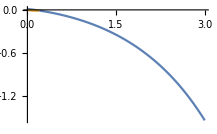
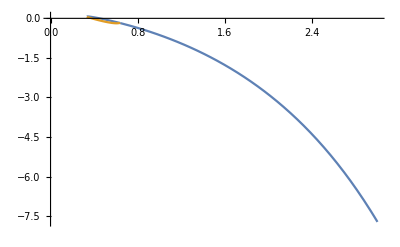
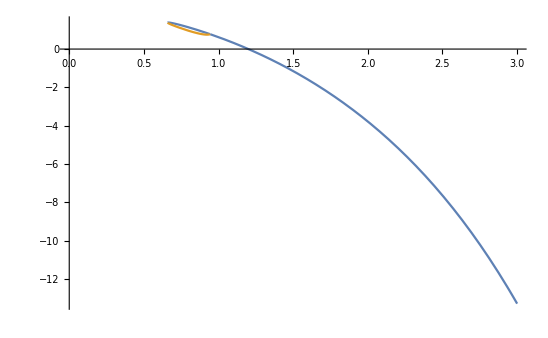
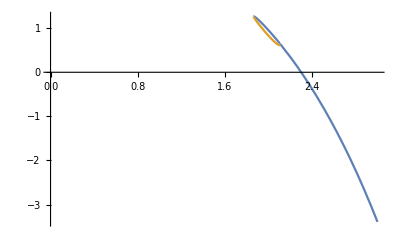
{{<|Location→0,Scale→1,Shape→0.2|>,Estimates→{0.622572,1/2,0.208333},-Graphics-},{<|Location→1,Scale→2,Shape→0.45|>,Estimates→{3.02864,2,2.93237},-Graphics-},{<|Location→2,Scale→3,Shape→1.2|>,Estimates→{7.52959,7/2,8.28571},-Graphics-},{<|Location→0.5,Scale→1.5,Shape→2.3|>,Estimates→{6.0277,1.25,0.816038},-Graphics-}}

```mathematica
{
CEParameters[[;;,#]],
"Estimates"->CEMoments[[;;,#]],
Plot[Evaluate[
{CEMoments[[1,#]]-GeoMeanCE[μ,σ,κ]/.MPSMTSolution[CEMoments[[2,#]],CEMoments[[3,#]]][[1]],
CEMoments[[1,#]]-GeoMeanCE[μ,σ,κ]/.MPSMTSolution[CEMoments[[2,#]],CEMoments[[3,#]]][[2]] 
}
],
{κ,0,3}
]
}&/@{1,2,3,4}
```

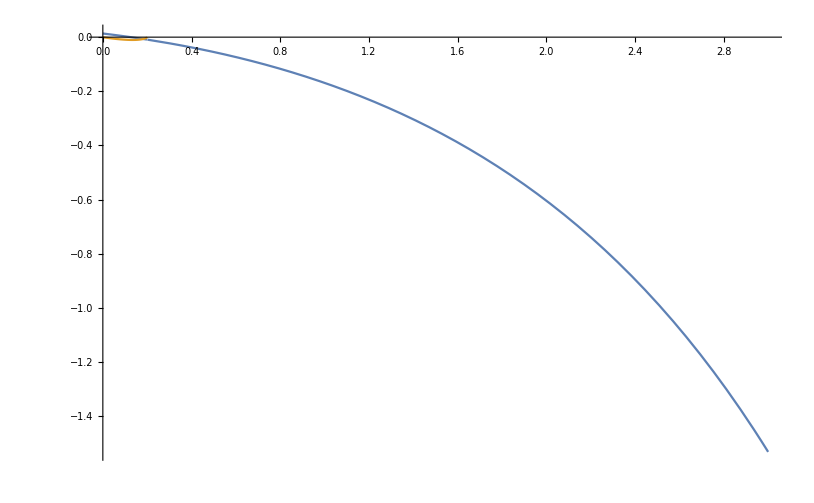
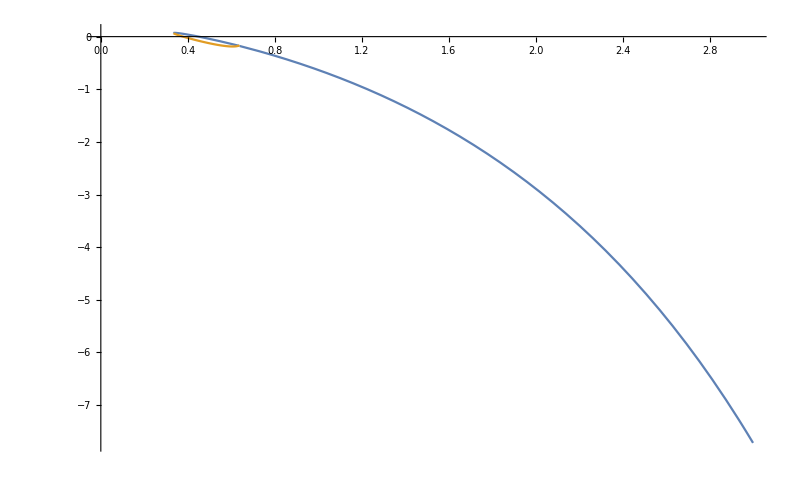
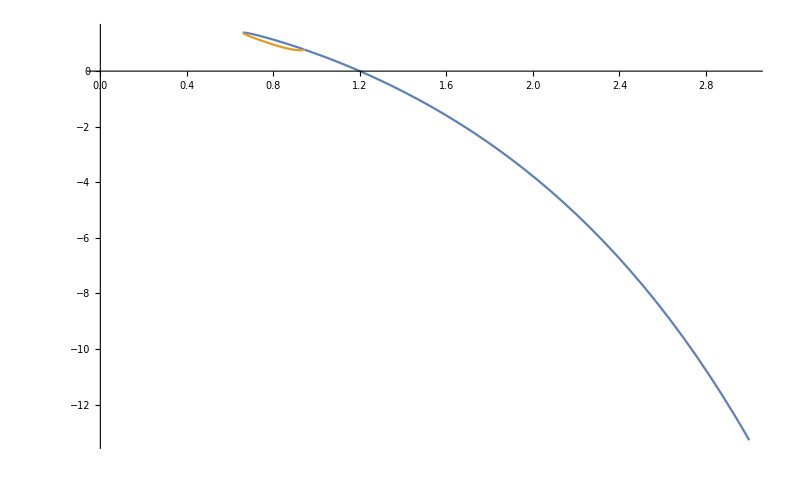
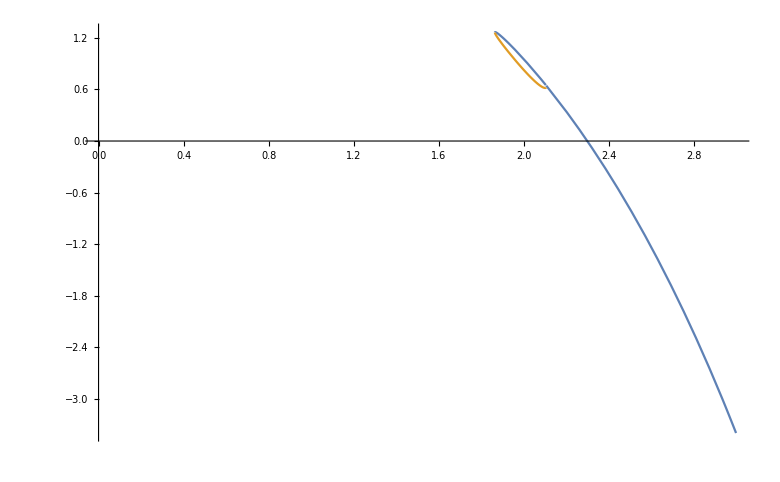
```mathematica
{{<|"Location"->0,"Scale"->1,"Shape"->0.2|>,"Estimates"->{0.6225723572206148,1/2,0.20833333333333331},
-Graphics-},{<|"Location"->1,"Scale"->2,"Shape"->0.45|>,"Estimates"->{3.0286437578445065,2,2.932367149758454},-Graphics-},{<|"Location"->2,"Scale"->3,"Shape"->1.2|>,"Estimates"->{7.5295850812903895,7/2,8.285714285714285},-Graphics-},{<|"Location"->0.5,"Scale"->1.5,"Shape"->2.3|>,"Estimates"->{6.027702112865905,1.25,0.8160377358490567},-Graphics-}}
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Greater::nord: Invalid comparison with 0.199993+0.130907 ⅈ attempted.

Greater::nord: Invalid comparison with 0.192907+0.105582 ⅈ attempted.

Greater::nord: Invalid comparison with 0.186305+0.0740131 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with 0.199993-0.130907 ⅈ attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

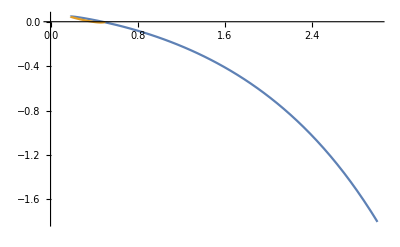
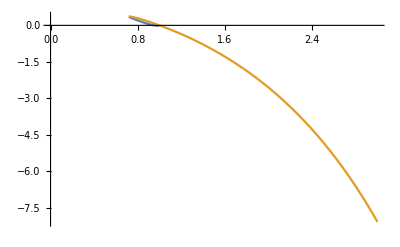
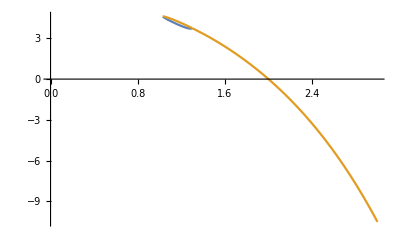
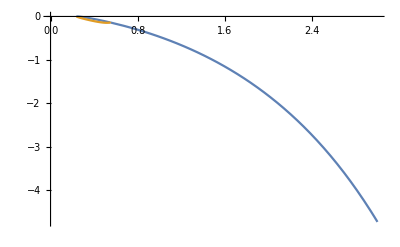
{{<|Location→0,Scale→1,Shape→0.5|>,Estimates→{0.735759,1/2,0.190476},-Graphics-},{<|Location→1,Scale→2,Shape→1|>,Estimates→{4,2,8/3},-Graphics-},{<|Location→2,Scale→3,Shape→2|>,Estimates→{2 ⅇ^(π/(√3)),7/2,38/5},-Graphics-},{<|Location→0.5,Scale→1.5,Shape→0.25|>,Estimates→{1.76697,1.25,1.17308},-Graphics-}}

#### Saved Images

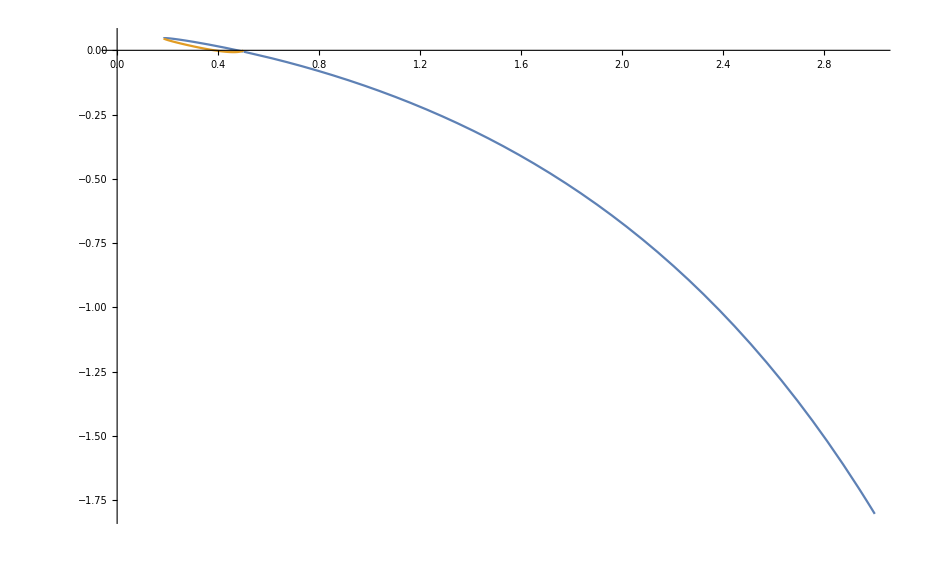
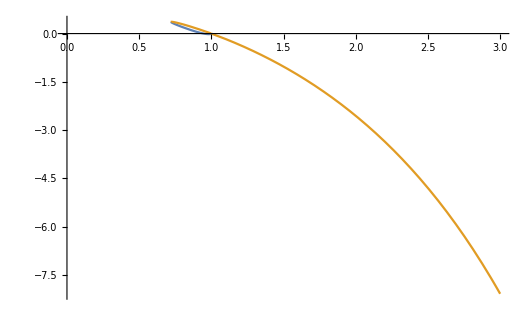
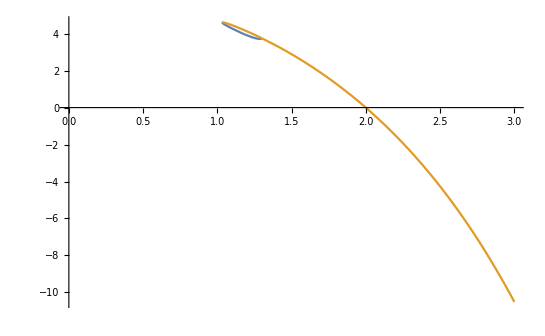
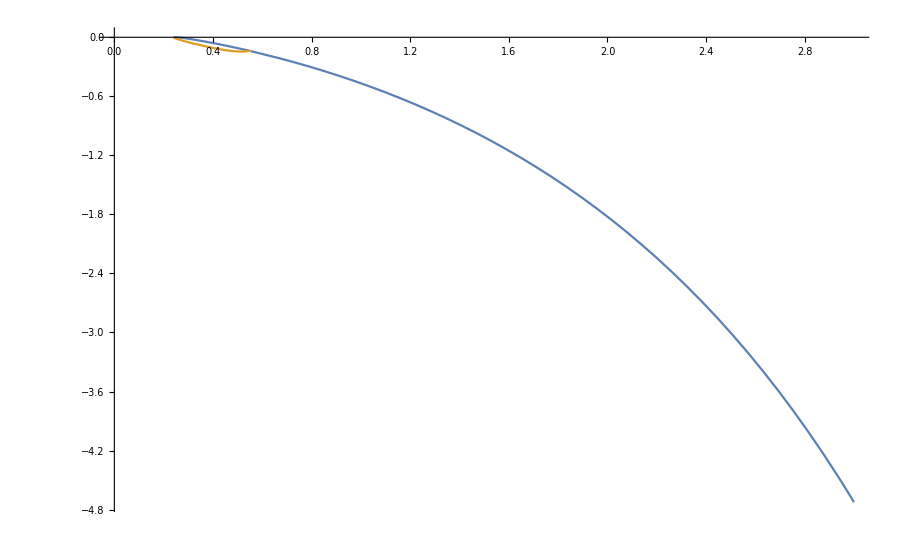
```mathematica
{{<|"Location"->0,"Scale"->1,"Shape"->0.5|>,"Estimates"->{0.7357588823428847,1/2,0.19047619047619047},-Graphics-},
{<|"Location"->1,"Scale"->2,"Shape"->1|>,"Estimates"->{4,2,8/3},-Graphics-},{<|"Location"->2,"Scale"->3,"Shape"->2|>,"Estimates"->{2 ⅇ^(π/(√3)),7/2,38/5},
-Graphics-},{<|"Location"->0.5,"Scale"->1.5,"Shape"->0.25|>,"Estimates"->{1.7669735918411253,1.25,1.1730769230769231},
-Graphics-}}
```

```mathematica
{{<|"Location"->0,"Scale"->1,"Shape"->0.2|>,"Estimates"->{0.6225723572206148,1/2,0.20833333333333331},
-Graphics-},{<|"Location"->1,"Scale"->2,"Shape"->0.45|>,"Estimates"->{3.0286437578445065,2,2.932367149758454},-Graphics-},{<|"Location"->2,"Scale"->3,"Shape"->1.2|>,"Estimates"->{7.5295850812903895,7/2,8.285714285714285},-Graphics-},{<|"Location"->0.5,"Scale"->1.5,"Shape"->2.3|>,"Estimates"->{6.027702112865905,1.25,0.8160377358490567},-Graphics-}}
```

#### Numerical Solution of Parameters starting with solution to GeoMean; substituting for location & scale

```mathematica
Clear[EstimateCEParameters];
SetAttributes[EstimateCEParameters,Listable];
EstimateCEParameters[GeoMeanEst_,MeanPairEst_,SecondMomentTripletsEst_]:=
EstimateCEParameters[GeoMeanEst,MeanPairEst,SecondMomentTripletsEst]=
Module[{},
NSolve[
GeoMeanEst==FullSimplify[GeoMeanCE[MPSMTSolution[MeanPairEst,SecondMomentTripletsEst][[1,1,2]],
MPSMTSolution[MeanPairEst,SecondMomentTripletsEst][[1,2,2]],κ],
0<κ<∞],
κ,
Reals]
];
```

```mathematica
EstimateCEParameters[{0.7357588823428847,4,2 ⅇ^(π/(√3))},{1/2,2,7/2},{0.19047619047619047,8/3,38/5}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

{NSolve[ConditionalExpression[0.735759==(Piecewise[{{Piecewise[{{0.5 ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(0.5 κ (1.-1. ((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2))))/((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2))]) (1.-1. ((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2))), κ>0}, {0.5 ⅇ^(-π (-1+(0.5 κ (1.-1. ((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2))))/((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2)))^(-1/κ) Csc[π/κ]+κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(0.5 κ (1.-1. ((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2))))/((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2))]) (1.-1. ((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2))), -1≤κ<0}, {0.5 ⅇ^(-ⅇ^((0.5 (1.-1. ((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2))))/((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2))) ExpIntegralEi[-(0.5 (1.-1. ((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2))))/((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2))]) (1.-1. ((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2))), κ==0}, {Not a Distribution, True}}], 0.5 (1.-1. ((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2)))>0}, {Piecewise[{{(ⅇ^(-HarmonicNumber[-1+1/κ]) ((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2)))/κ, κ>0}, {-(ⅇ^(κ-HarmonicNumber[-(1+κ)/κ]) ((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2)))/κ, -1≤κ<0}, {ⅇ^-EulerGamma ((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2)), κ==0}, {Not a Distribution, True}}], 0.5 (1.-1. ((3. (1.+κ))/(5.+3. κ)-0.755929 √((-3.+14. κ+12. κ^2)/(5.+3. κ)^2)))==0}, {Not a Distribution, True}}]), ],κ,ℝ],NSolve[ConditionalExpression[4==(Piecewise[{{Piecewise[{{ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (2+1/2 (-(12 (1+κ))/(5+3 κ)-4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2))))/((12 (1+κ))/(5+3 κ)+4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2))]) (2+1/2 (-(12 (1+κ))/(5+3 κ)-4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2))), κ>0}, {ⅇ^(-π (-1+(κ (2+1/2 (-(12 (1+κ))/(5+3 κ)-4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2))))/((12 (1+κ))/(5+3 κ)+4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2)))^(-1/κ) Csc[π/κ]+κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (2+1/2 (-(12 (1+κ))/(5+3 κ)-4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2))))/((12 (1+κ))/(5+3 κ)+4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2))]) (2+1/2 (-(12 (1+κ))/(5+3 κ)-4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2))), -1≤κ<0}, {ⅇ^(-ⅇ^((2+1/2 (-(12 (1+κ))/(5+3 κ)-4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2)))/((12 (1+κ))/(5+3 κ)+4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2))) ExpIntegralEi[-(2+1/2 (-(12 (1+κ))/(5+3 κ)-4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2)))/((12 (1+κ))/(5+3 κ)+4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2))]) (2+1/2 (-(12 (1+κ))/(5+3 κ)-4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2))), κ==0}, {Not a Distribution, True}}], 2+1/2 (-(12 (1+κ))/(5+3 κ)-4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2))>0}, {Piecewise[{{(ⅇ^(-HarmonicNumber[-1+1/κ]) ((12 (1+κ))/(5+3 κ)+4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2)))/κ, κ>0}, {-(ⅇ^(κ-HarmonicNumber[-(1+κ)/κ]) ((12 (1+κ))/(5+3 κ)+4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2)))/κ, -1≤κ<0}, {ⅇ^-EulerGamma ((12 (1+κ))/(5+3 κ)+4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2)), κ==0}, {Not a Distribution, True}}], 2+1/2 (-(12 (1+κ))/(5+3 κ)-4 √2 √((-3+2 κ+3 κ^2)/(5+3 κ)^2))==0}, {Not a Distribution, True}}]), ],κ,ℝ],NSolve[ConditionalExpression[2 ⅇ^(π/(√3))==(Piecewise[{{Piecewise[{{1/2 ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (7-(21 (1+κ))/(5+3 κ)-(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5)))/(2 ((21 (1+κ))/(5+3 κ)+(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5)))]) (7-(21 (1+κ))/(5+3 κ)-(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5)), κ>0}, {1/2 ⅇ^(-π (-1+(κ (7-(21 (1+κ))/(5+3 κ)-(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5)))/(2 ((21 (1+κ))/(5+3 κ)+(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5))))^(-1/κ) Csc[π/κ]+κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (7-(21 (1+κ))/(5+3 κ)-(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5)))/(2 ((21 (1+κ))/(5+3 κ)+(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5)))]) (7-(21 (1+κ))/(5+3 κ)-(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5)), -1≤κ<0}, {1/2 ⅇ^(-ⅇ^((7-(21 (1+κ))/(5+3 κ)-(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5))/(2 ((21 (1+κ))/(5+3 κ)+(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5)))) ExpIntegralEi[-(7-(21 (1+κ))/(5+3 κ)-(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5))/(2 ((21 (1+κ))/(5+3 κ)+(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5)))]) (7-(21 (1+κ))/(5+3 κ)-(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5)), κ==0}, {Not a Distribution, True}}], 1/2 (7-(21 (1+κ))/(5+3 κ)-(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5))>0}, {Piecewise[{{(ⅇ^(-HarmonicNumber[-1+1/κ]) ((21 (1+κ))/(5+3 κ)+(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5)))/κ, κ>0}, {-(ⅇ^(κ-HarmonicNumber[-(1+κ)/κ]) ((21 (1+κ))/(5+3 κ)+(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5)))/κ, -1≤κ<0}, {ⅇ^-EulerGamma ((21 (1+κ))/(5+3 κ)+(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5)), κ==0}, {Not a Distribution, True}}], 1/2 (7-(21 (1+κ))/(5+3 κ)-(6 √((-55+14 κ+38 κ^2)/(5+3 κ)^2))/(√5))==0}, {Not a Distribution, True}}]), ],κ,ℝ]}

```mathematica
EstimateCEParameters[0.7357588823428847,1/2,0.19047619047619047]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolve[ConditionalExpression[0.735759==(Piecewise[{{Not a Distribution, κ<-1}, {(ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1+κ (0.5+(3.30719+1.98431 κ)/(-3.96863-3.96863 κ+1. √(-3.+κ (14.+12. κ))))]) (0.333333+0.125988 √(-3.+κ (14.+12. κ))))/(1.66667+1. κ), True}}]), κ>0.184962||κ<-1.35163],κ,ℝ]

```mathematica
NSolve[0.7357588823428847==(ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1+κ (0.5+(3.307189138830739+1.984313483298443 κ)/(-3.968626966596886-3.968626966596886 κ+1. √(-3.+κ (14.+12. κ))))]) (0.33333333333333337+0.1259881576697424 √(-3.+κ (14.+12. κ))))/(1.6666666666666667+1. κ),κ,Reals]
```

NSolve[0.735759==(ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1+κ (0.5+(3.30719+1.98431 κ)/(-3.96863-3.96863 κ+1. √(-3.+κ (14.+12. κ))))]) (0.333333+0.125988 √(-3.+κ (14.+12. κ))))/(1.66667+1. κ),κ,ℝ]

```mathematica
EstimateCEParameters[4,2,8/3]
```

{}

```mathematica
EstimateCEParameters[2 ⅇ^(π/(√3)),7/2,38/5]
```

{}

```mathematica
MeanPairEst==MeanPairsCE[μ,σ],
SecondMomentTripletsEst=SecondMomentTripletsCE[μ,σ,κ]
},
```

### Examine Approximations for the HyperGeometric Function

The attempts to use NSolve, even on approximations of the HyperGeometric function ran for over 24 hrs without a solution

From StackExchange
 https://math.stackexchange.com/questions/718442/approximating-hypergeometric-function-f1-1a-2a-z-for-z-1
-Graphics-
Focusing on the domain μ > 0 and κ > 0,  GeoMean = ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ])μ
From the equation above, a = 1/κ-1, z = 1-(κ μ)/σ

```mathematica
GeoMeanApprox[μ_,σ_,κ_]:=GeoMeanApprox[μ,σ,κ]=
μ Exp[-1/(1-(κ μ)/σ)^(1/κ)(Log[(κ μ)/σ]+HarmonicNumber[1/κ-1]+∑_(n=1)^0 (Binomial[1/κ-1,n](-(κ μ)/σ)^n)/n)];
```

```mathematica
Clear[EstimateCEParameters];
SetAttributes[EstimateCEParameters,Listable];
EstimateCEParameters[GeoMeanEst_,MeanPairEst_,SecondMomentTripletsEst_]:=
EstimateCEParameters[GeoMeanEst,MeanPairEst,SecondMomentTripletsEst]=
Module[{},
NSolve[
GeoMeanEst==FullSimplify[GeoMeanApprox[MPSMTSolution[MeanPairEst,SecondMomentTripletsEst][[1,1,2]],
MPSMTSolution[MeanPairEst,SecondMomentTripletsEst][[1,2,2]],κ],
0<κ<∞],
κ,
Reals]
];
```

```mathematica
Clear[MPSMTSolution,MeanPairEst,SecondMomentTripletsEst];
MPSMTSolution[MeanPairEst_,SecondMomentTripletsEst_]:=
FullSimplify[
Solve[{
MeanPairEst==μ+σ/2,
SecondMomentTripletsEst==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ))},
{μ,σ},
Reals],
0<κ<∞]
```

```mathematica
CEParameters = <|
"Location" ->{0.1,1,2,0.5},
"Scale" ->{1,2,3,1.5},
"Shape" ->{0.2,0.45,1.2,1.8}
|>
CEMoments =
{GeoMeanCE[#Location,#Scale,#Shape],MeanPairsCE[#Location,#Scale],SecondMomentTripletsCE[#Location,#Scale,#Shape]}&[
CEParameters
]
```

<|Location→{0.1,1,2,0.5},Scale→{1,2,3,1.5},Shape→{0.2,0.45,1.2,1.8}|>

{GeoMeanCE[{0.1,1,2,0.5},{1,2,3,1.5},{0.2,0.45,1.2,1.8}],MeanPairsCE[{0.1,1,2,0.5},{1,2,3,1.5}],SecondMomentTripletsCE[{0.1,1,2,0.5},{1,2,3,1.5},{0.2,0.45,1.2,1.8}]}

```mathematica
EstimateCEParameters[CEMoments[[1]],CEMoments[[2]],CEMoments[[3]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

### Can the GeoMean Equation be split into components to simplify solution?

GeoMeanEst=ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ])μ
1/κ Log[GeoMeanEst/μ]=Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]

Plot the two expressions to explore approaches to solving equation

```mathematica
PlotGeoMeanComponents[GeoMeanEst_,MeanPairEst_,SecondMomentTripletsEst_,CEParams_]:=
Plot[{
1/κ Log[GeoMeanEst/μ]/.MPSMTSolution[MeanPairEst,SecondMomentTripletsEst],
Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]/.MPSMTSolution[MeanPairEst,SecondMomentTripletsEst]},
{κ,0,2},
PlotRange->{{0,2},{0,10}},
Epilog->{Directive[{Thick,Red,Dashed}], Line[{{CEParams[["Shape"]],0},{CEParams[["Shape"]],10}}]},
AxesLabel->{"κ","f(κ)"},
PlotLabel->CEParams
]
```

```mathematica
PlotGeoMeanComponents[CEMoments[[1,#]],CEMoments[[2,#]],CEMoments[[3,#]],CEParameters[[;;,#]]]&/@{1,2,3,4}
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

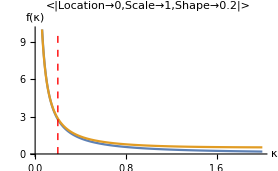
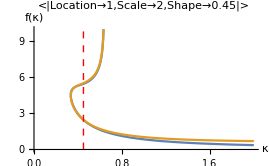
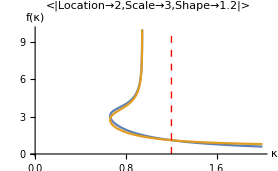
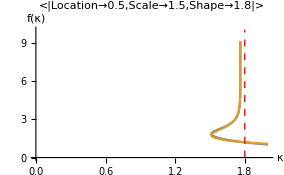

Modify the GeoMean equation to be a function of μ instead of κ. Perhaps GeoMean is more sensitive to μ and therefore shows less of the dependency evident in the above plots.

```mathematica
Clear[MPSMTforLoc,MeanPairEst,SecondMomentTripletsEst];
MPSMTforLoc[MeanPairEst_,SecondMomentTripletsEst_]:=
FullSimplify[
Solve[{
MeanPairEst==μ+σ/2,
SecondMomentTripletsEst==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ))},
{σ,κ},
Reals],
0<μ<∞]
```

```mathematica
PlotGeoMeanVsLocation[GeoMeanEst_,MeanPairEst_,SecondMomentTripletsEst_,CEParams_]:=
Plot[{
1/κ Log[GeoMeanEst/μ]/.MPSMTforLoc[MeanPairEst,SecondMomentTripletsEst],
Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]/.MPSMTforLoc[MeanPairEst,SecondMomentTripletsEst]},
{μ,0,3},
PlotRange->{{0,3},{0,10}},
Epilog->{Directive[{Thick,Red,Dashed}], Line[{{CEParams[["Location"]],0},{CEParams[["Location"]],10}}]},
AxesLabel->{"μ","f(μ)"},
PlotLabel->CEParams
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

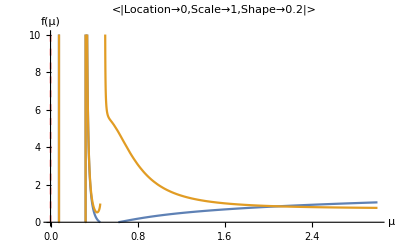
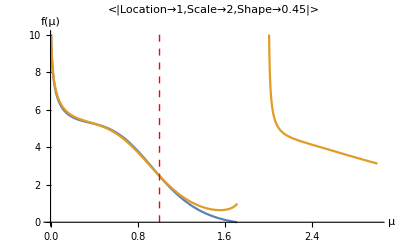
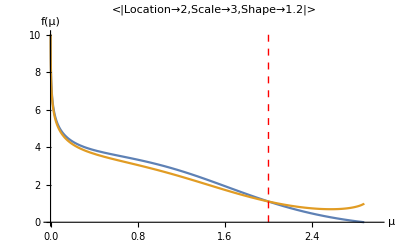
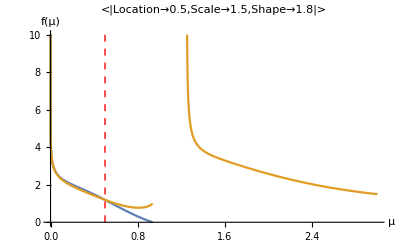

```mathematica
PlotGeoMeanVsLocation[CEMoments[[1,#]],CEMoments[[2,#]],CEMoments[[3,#]],CEParameters[[;;,#]]]&/@{1,2,3,4}
```

```mathematica
Clear[MPSMTforScale,MeanPairEst,SecondMomentTripletsEst];
MPSMTforScale[MeanPairEst_,SecondMomentTripletsEst_]:=
FullSimplify[
Solve[{
MeanPairEst==μ+σ/2,
SecondMomentTripletsEst==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ))},
{μ,κ},
Reals],
0<σ<∞]
```

```mathematica
PlotGeoMeanVsScale[GeoMeanEst_,MeanPairEst_,SecondMomentTripletsEst_,CEParams_]:=
Plot[{
1/κ Log[GeoMeanEst/μ]/.MPSMTforScale[MeanPairEst,SecondMomentTripletsEst],
Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]/.MPSMTforScale[MeanPairEst,SecondMomentTripletsEst]},
{σ,0,4},
PlotRange->{{0,4},{0,10}},
Epilog->{Directive[{Thick,Red,Dashed}], Line[{{CEParams[["Scale"]],0},{CEParams[["Scale"]],10}}]},
AxesLabel->{"σ","f(σ)"},
PlotLabel->CEParams
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

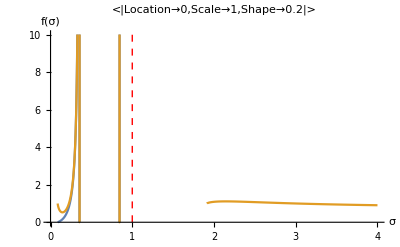
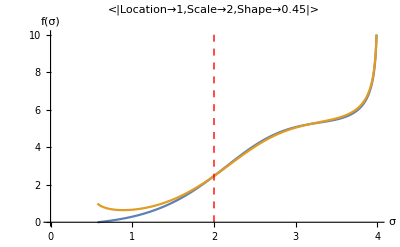
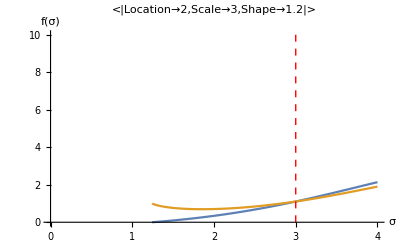
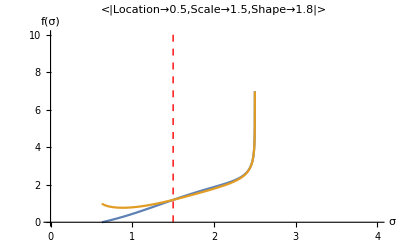

```mathematica
PlotGeoMeanVsScale[CEMoments[[1,#]],CEMoments[[2,#]],CEMoments[[3,#]],CEParameters[[;;,#]]]&/@{1,2,3,4}
```

### Is it possible to remove the dependency between the two functions using the expansion of the Hypergeometric function?

Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]=(-1/κ)/(1-(κ μ)/σ)^(1/κ)(Log[(κ μ)/σ]+HarmonicNumber[1/κ-1]+∑_(n=1)^N (Binomial[1/κ-1,n](-(κ μ)/σ)^n)/n)
must equal 1/κ Log[GeoMeanEst/μ]= 1/κ Log[GeoMeanEst] - 1/κ Log[μ],
so the 1/κ can be factored out and term - 1/κLog[μ] can be eliminated ; this log term has some other multiplying factors
factoring out 1/κ first gives
Log[GeoMeanEst] - Log[μ] = -1/(1-(κ μ)/σ)^(1/κ)(Log[(κ μ)/σ]+HarmonicNumber[1/κ-1]+∑_(n=1)^N (Binomial[1/κ-1,n](-(κ μ)/σ)^n)/n)

Log[GeoMeanEst] = Log[μ]-Log[u]/(1-(κ μ)/σ)^(1/κ)+-1/(1-(κ μ)/σ)^(1/κ)(Log[κ/σ]+HarmonicNumber[1/κ-1]+∑_(n=1)^N (Binomial[1/κ-1,n](-(κ μ)/σ)^n)/n)

The expression does not simplify very much but it does suggest comparing the Log[GeoMean] with the expression κ HG[ ...] + Log[μ]

```mathematica
PlotGeoMeanComponents[GeoMeanEst_,MeanPairEst_,SecondMomentTripletsEst_,CEParams_]:=
Plot[{
Log[GeoMeanEst],
(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]+Log[μ])/.MPSMTSolution[MeanPairEst,SecondMomentTripletsEst]},
{κ,0,2},
PlotRange->{{0,2},{0,10}},
Epilog->{Directive[{Thick,Red,Dashed}], Line[{{CEParams[["Shape"]],0},{CEParams[["Shape"]],10}}]},
AxesLabel->{"κ","f(κ)"},
PlotLabel->CEParams
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

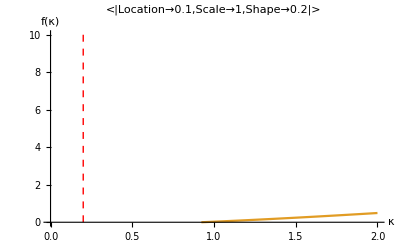
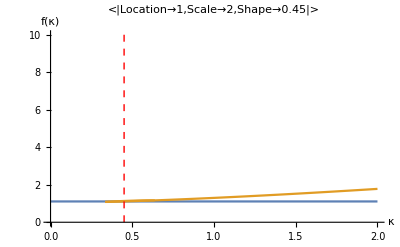
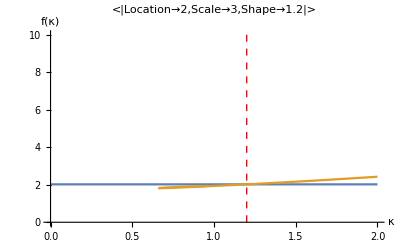
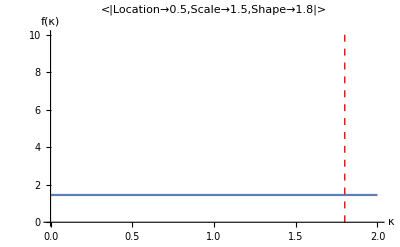

```mathematica
PlotGeoMeanComponents[CEMoments[[1,#]],CEMoments[[2,#]],CEMoments[[3,#]],CEParameters[[;;,#]]]&/@{1,2,3,4}
```

These plots also show the extreme similarity between the two expressions.  Not surprising, since this didn’t change the expression but just rearranged the terms.

Now using the approximation is there any difference?

```mathematica
PlotGeoMeanComponents[GeoMeanEst_,MeanPairEst_,SecondMomentTripletsEst_,CEParams_]:=
Plot[{
Log[GeoMeanEst],
(Log[μ]-Log[μ]/(1-(κ μ)/σ)^(1/κ)+-1/(1-(κ μ)/σ)^(1/κ)(Log[κ/σ]+HarmonicNumber[1/κ-1]+∑_(n=1)^10 (Binomial[1/κ-1,n](-(κ μ)/σ)^n)/n))/.MPSMTSolution[MeanPairEst,SecondMomentTripletsEst]},
{κ,0,2},
(* PlotRange->{{0,2},{0,10}}, *)
Epilog->{Directive[{Thick,Red,Dashed}], Line[{{CEParams[["Shape"]],0},{CEParams[["Shape"]],10}}]},
AxesLabel->{"κ","f(κ)"},
PlotLabel->CEParams
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

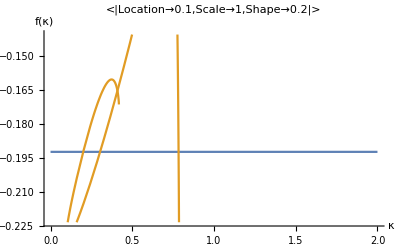
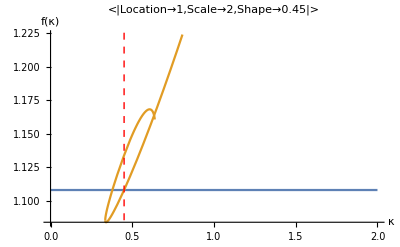
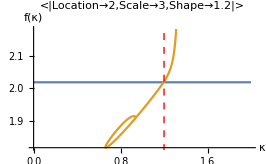
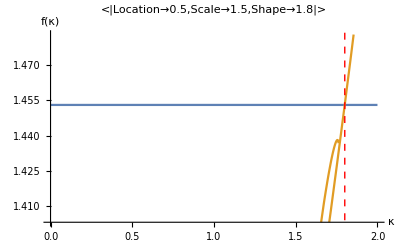

```mathematica
PlotGeoMeanComponents[CEMoments[[1,#]],CEMoments[[2,#]],CEMoments[[3,#]],CEParameters[[;;,#]]]&/@{1,2,3,4}
```

```mathematica
PlotGeoMeanComponents[GeoMeanEst_,MeanPairEst_,SecondMomentTripletsEst_,CEParams_]:=
Plot[{
Log[GeoMeanEst],
(Log[μ]-Log[μ]/(1-(κ μ)/σ)^(1/κ)+-1/(1-(κ μ)/σ)^(1/κ)(Log[κ/σ]+HarmonicNumber[1/κ-1]+∑_(n=1)^100 (Binomial[1/κ-1,n](-(κ μ)/σ)^n)/n))/.MPSMTSolution[MeanPairEst,SecondMomentTripletsEst]},
{κ,0,2},
(* PlotRange->{{0,2},{0,10}}, *)
Epilog->{Directive[{Thick,Red,Dashed}], Line[{{CEParams[["Shape"]],0},{CEParams[["Shape"]],10}}]},
AxesLabel->{"κ","f(κ)"},
PlotLabel->CEParams
]
```

General::munfl: (-0.0000408571)^71 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-0.0000408571)^72 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-0.0000408571)^73 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

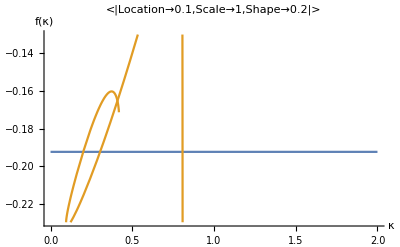
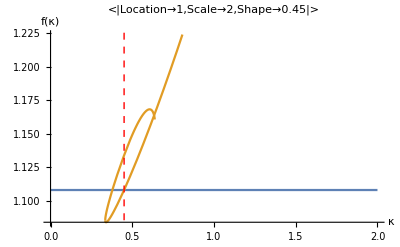
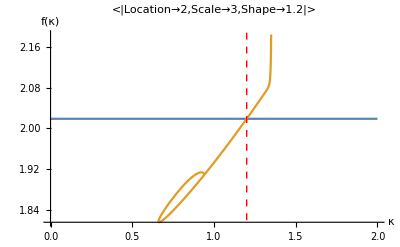
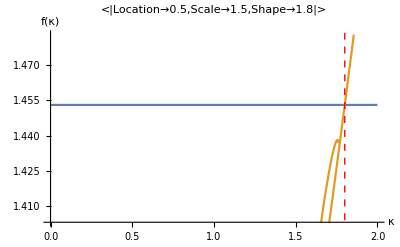

```mathematica
PlotGeoMeanComponents[CEMoments[[1,#]],CEMoments[[2,#]],CEMoments[[3,#]],CEParameters[[;;,#]]]&/@{1,2,3,4}
```

The plots are so different that I’m skeptical that the approximation function is valid.

### Case with μ = 0

GeoMean = (ⅇ^(-HarmonicNumber[-1+1/κ]) σ)/κ and MeanPairs = σ/2
The function FindRoot but not Solve or NSolve is successful in determining κ given the GeoMean and the MeanPairs

```mathematica
CEParameters = <|
"Location" ->{0,0,0,0},
"Scale" ->{1,2,3,1.5},
"Shape" ->{0.2,0.45,1.2,1.8}
|>
CEMoments =
{GeoMeanCE[#Location,#Scale,#Shape],MeanPairsCE[#Location,#Scale],SecondMomentTripletsCE[#Location,#Scale,#Shape]}&[
CEParameters
]
```

<|Location→{0,0,0,0},Scale→{1,2,3,1.5},Shape→{0.2,0.45,1.2,1.8}|>

{{0.622572,1.42974,3.42056,2.5942},{1/2,1,3/2,0.75},{0.208333,0.772947,1.42857,0.3125}}

```mathematica
PlotGeoMeanComponentsMu0[GeoMeanEst_,MeanPairEst_,SecondMomentTripletsEst_,CEParams_]:=
Plot[{
 Log[GeoMeanEst κ/(2 MeanPairEst)],
-HarmonicNumber[1/κ-1]
},
{κ,0,2},
 (*PlotRange->{{0,2},{0,10}},*)
Epilog->{Directive[{Thick,Red,Dashed}], Line[{{CEParams[["Shape"]],0},{CEParams[["Shape"]],10}}]},
AxesLabel->{"κ","f(κ)"},
PlotLabel->CEParams
]
```

```mathematica
PlotGeoMeanComponentsMu0[CEMoments[[1,#]],CEMoments[[2,#]],CEMoments[[3,#]],CEParameters[[;;,#]]]&/@{1,2,3,4}
```

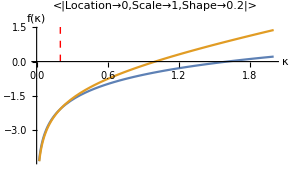
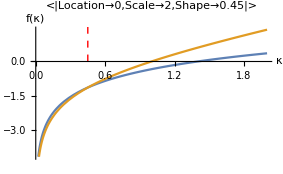
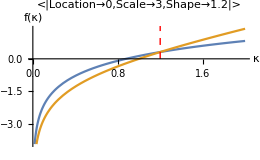
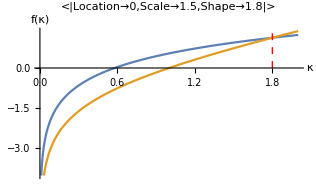

```mathematica
Clear[EstimateCEScaleShape];
SetAttributes[EstimateCEScaleShape,Listable];
EstimateCEScaleShape[GeoMeanEst_,MeanPairEst_]:=
EstimateCEScaleShape[GeoMeanEst,MeanPairEst]=
Module[{κEst},
κEst =FindRoot[
GeoMeanEst==FullSimplify[GeoMeanCE[0,2 MeanPairEst,κ],
0<κ<∞],
{κ,1}];
<|"σ"->2MeanPairEst,κEst|>
];
```

```mathematica
EstimateCEScaleShape[CEMoments[[1]],CEMoments[[2]]]
```

{<|σ→1,κ→0.2|>,<|σ→2,κ→0.45|>,<|σ→3,κ→1.2|>,<|σ→1.5,κ→1.8|>}